```mathematica
Quit[]
```

Import data from txt file.  Strip out the stupid stuff. Leaves list of pulse heights.

```mathematica
rawdata = Import["/Users/stevenschowalter/desktop/mms2-19electron_height3.txt.txt","Data"];
rawdata = Flatten[Take[rawdata,All,{3}]];
```

Bin the data->histogram with bin sizes of "binwidth"

```mathematica
{num}=Dimensions[rawdata];
binwidth=.01;
k=0;
x=1;
bins=Table[0,{i,2/binwidth}];
Do[
{
Do[
If[rawdata[[i]]≥k*binwidth&&rawdata[[i]]<(k+1)*binwidth,
{
x++;
}
],{i,1,num}];
bins[[k+1]]={(2k+1)/2*binwidth,x};
x=0;
}
,{k,0,2/binwidth-1}
]
```

Plot the raw data (histogram)...if you want.

```mathematica
data =ListPlot[bins,PlotRange->All,Joined->True];
```

Do a nonlinear regression test to fit the data (excluding the first 20 bins) to an exponential decay

```mathematica
Needs["NonlinearRegression`"]
```

```mathematica
ans=NonlinearRegress[Drop[bins,20],A ⅇ^(- t/τ),{A,τ},t]
```

{BestFitParameters→{A→79.8105,τ→0.251723},ParameterCITable→ | Estimate | Asymptotic SE | CI
A | 79.8105 | 4.55277 | {70.8262,88.7949}
τ | 0.251723 | 0.0103461 | {0.231306,0.272139},EstimatedVariance→6.90472,ANOVATable→ | DF | SumOfSq | MeanSq
Model | 2 | 16360. | 8179.98
Error | 178 | 1229.04 | 6.90472
Uncorrected Total | 180 | 17589. | 
Corrected Total | 179 | 12958.1 | ,AsymptoticCorrelationMatrix→(1. | -0.9329
-0.9329 | 1.),FitCurvatureTable→ | Curvature
Max Intrinsic | 0.0579718
Max Parameter-Effects | 0.483361
95. % Confidence Region | 0.572906}

Store the fit parameters

```mathematica
τ=τ/.Take[BestFitParameters/.ans[[1]],{2}];
```

```mathematica
A=A/.Take[BestFitParameters/.ans[[1]],{1}];
```

Plot the data and fit...how pretty! (not really)

```mathematica
fit=Plot[A ⅇ^(- t/τ),{t,0,2}];
```

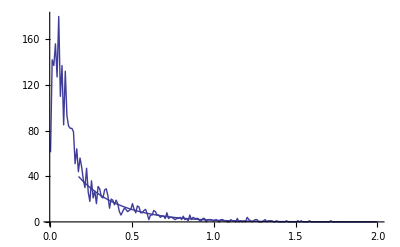

```mathematica
Show[data,fit]
```

Store the 95% parameter errors

```mathematica
δA=(Flatten[Take[Flatten[ParameterCITable/.ans[[2]]][[1]],All,-1][[1]]][[2]]-Flatten[Take[Flatten[ParameterCITable/.ans[[2]]][[1]],All,-1][[1]]][[1]])/2;
```

```mathematica
δτ=(Flatten[Take[Flatten[ParameterCITable/.ans[[2]]][[1]],All,-1][[2]]][[2]]-Flatten[Take[Flatten[ParameterCITable/.ans[[2]]][[1]],All,-1][[2]]][[1]])/2;
```

Declare! functions for predicted height and height error for some "t" (which is an e height pulse) based on the fit parameters.

```mathematica
h[t_]:=A*ⅇ^(-t/τ)
δh[p_]:=√((-A/τ ⅇ^(-p/τ)δτ)^2+( ⅇ^(-p/τ)δA)^2)
```

Determine the first pulse height "t" where the 95% CI of the predicted point (h[t]+/-δh[t]) does not include 1 (h[t]-δh[t]<1).  Call this the energy cutoff. Yeah!?

```mathematica
Do[If[h[(2*i-1)/2*binwidth]+δh[(2*i-1)/2*binwidth]<1,{Print[bins[[i]][[1]]],Abort[]}],{i,1,2/binwidth}]
```

1.145

$Aborted